```mathematica
SDATA={
CI->1.5 10^6,
TW->0.170,
TL-> 1.5,
g-> 9.81,
𝒟-> TL/2,
d-> 0.410/2,
h->0.0,
d1-> 0.740,
d2-> 0.330,
m0->212.3+340.1,
m1->316.3,
m2->47.5,
m4->316.3,
Jz0->44.3,
Jz1-> 24.05,
Jz2->0.71,
Jz4-> 24.05,
k-> 5.0 10^6,
b->28000.0,
IF-> 5286.0,
vd-> 2.0,
sd-> 0.047787558339910864,
ωd-> vd/(d1/2(1-sd)),
λ->  2.5,
vmin->0.0001,
ωmin-> vmin/(d1/2),
vymin-> -1.0 10^-6
};
```

```mathematica
m={m0,m1,m2,m2,m4};
Jz={Jz0,Jz1,Jz2,Jz2,Jz4};
M[i_]:={{m⟦i+1⟧,0,0},{0,m⟦i+1⟧,0},{0,0,Jz⟦i+1⟧}};
r={0,1, d1/d2, d1/d2,1};
X={0,𝒟,d,-d,-𝒟};
Y={h,0,(d2-d1)/2,(d2-d1)/2,0};
ξ[t_]={x[t],y[t],α[t],θ[t]};
q[i_]:={x[t]+Cos[α[t]] X⟦i+1⟧-Sin[α[t]] Y⟦i+1⟧,y[t]+Sin[α[t]] X⟦i+1⟧+Cos[α[t]] Y⟦i+1⟧,α[t] -r⟦i+1⟧ θ[t]};
J[i_]:=D[q[i], {ξ[t]}];
dJ[i_]:=D[J[i], t];
𝕄=Simplify[∑_(i=0)^4 J[i]ᵀ.M[i].J[i]];
𝕧=Simplify[(∑_(i=0)^4 J[i]ᵀ.M[i].dJ[i]).ξ'[t]];
𝕘=Simplify[(∑_(i=0)^4 J[i]ᵀ.{0,m⟦i+1⟧g,0})];
W = TW TL Cos[α[t]](k(d1/2-y[t])+b(0-y'[t]));
s = 1 - (2 x'[t])/(d1 θ'[t]);
DWR = 1 - (TL Sin[2α[t]])/(12(d1-y[t]));
Bn =Simplify[ (CI TW TL)/(W (1-Exp[-CI/(0.698 10^6)]))5/(1+6 TW/TL)];
DWI = 1 - Abs[(0.7(DWR-1))/(DWR+1)];
GTR = 1.10 (1-Exp[-0.025 Bn])(1-Exp[-17 s])+0.03/DWI;
MRR=2.5/(Bn DWI)+0.03/DWI+(0.5s)/(√Bn);
NTR = GTR - MRR;
TE = NTR/GTR(1-s);
GT = W GTR;
MR = W MRR;
NT = W NTR;
𝕗={
W(GTR Tanh[100 (d1/2 θ'[t]-x'[t])]-MRR Tanh[100 x'[t]] )Cos[α[t]]-IF Tanh[100 x'[t]],
W (1+(GTR Tanh[100 (d1/2 θ'[t]-x'[t])]-MRR Tanh[100 x'[t]] )Sin[α[t]]),
-k TW TL^3 Cos[α[t]]^2 Sin[α[t]],
τ[t]-(d1 W(GTR Tanh[100 (d1/2 θ'[t]-x'[t])]-MRR Tanh[100 x'[t]] ))/2
};
```

```mathematica
𝕄//MatrixForm
```

(m0+m1+2 m2+m4 | 0 | -((h m0+(-d1+d2) m2) Cos[α[t]])+(-m1+m4) 𝒟 Sin[α[t]] | 0
0 | m0+m1+2 m2+m4 | (m1-m4) 𝒟 Cos[α[t]]-(h m0+(-d1+d2) m2) Sin[α[t]] | 0
-((h m0+(-d1+d2) m2) Cos[α[t]])+(-m1+m4) 𝒟 Sin[α[t]] | (m1-m4) 𝒟 Cos[α[t]]-(h m0+(-d1+d2) m2) Sin[α[t]] | Jz0+Jz1+2 Jz2+Jz4+h^2 m0+2 d^2 m2+(d1^2 m2)/2-d1 d2 m2+(d2^2 m2)/2+m1 𝒟^2+m4 𝒟^2 | -(2 d1 Jz2+d2 (Jz1+Jz4))/d2
0 | 0 | -(2 d1 Jz2+d2 (Jz1+Jz4))/d2 | Jz1+(2 d1^2 Jz2)/d2^2+Jz4)

```mathematica
𝕧//MatrixForm
```

(-(((m1-m4) 𝒟 Cos[α[t]]-(h m0+(-d1+d2) m2) Sin[α[t]]) α'[t]^2)
-(((h m0+(-d1+d2) m2) Cos[α[t]]+(m1-m4) 𝒟 Sin[α[t]]) α'[t]^2)
0
0)

```mathematica
𝕘//MatrixForm
```

(0
g (m0+m1+2 m2+m4)
g ((m1-m4) 𝒟 Cos[α[t]]-(h m0+(-d1+d2) m2) Sin[α[t]])
0)

```mathematica
𝓅1[x_]=p1+(p2-p1)/TL x;
𝓅2[y_]=p2+(p1-p2)/TL y;
V1[𝓍_]=∫_0^𝓍 𝓅1[x]ⅆx;
V2[𝓎_]=∫_0^𝓎 𝓅2[y]ⅆy;
M1[𝓍_]=∫_0^𝓍 V1[x]ⅆx;
M2[𝓎_]=∫_0^𝓎 V2[y]ⅆy;
```

```mathematica
Simplify[(x/.Solve[M1[x]==M2[TL-x],x]⟦1,1⟧)-TL/2]
```

((-p1+p2) TL)/(6 (p1+p2))

```mathematica
Simplify[V1[TL/2]+V2[TL/2]]
```

1/2 (p1+p2) TL

```mathematica
Simplify[M2[TL/2]-M1[TL/2]]
```

1/12 (-p1+p2) TL^2

```mathematica
EQ=(𝕄. ξ''[t]+𝕧+𝕘-𝕗)/.τ[t]->𝕄⟦4,4⟧(2λ(ωd-θ'[t])+λ^2(ωd t - θ[t]));
sol=NDSolve[{EQ⟦1⟧==0,EQ⟦2⟧==0,EQ⟦3⟧==0,EQ⟦4⟧==0,θ[0]==0,α[0]==0,x[0]==0,y[0]==d1/2-0.00722,θ'[0]==ωmin,α'[0]==0,x'[0]==0,y'[0]==vymin}//.SDATA,Join[ξ[t],ξ'[t]],{t,0,20},Method->{"EquationSimplification"->"Residual"}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],α[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t],α'[t]→InterpolatingFunction[…][t],θ'[t]→InterpolatingFunction[…][t]}}

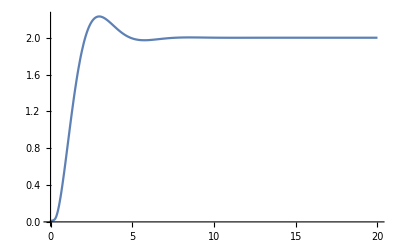

```mathematica
Plot[Evaluate[x'[t]/.sol],{t,0,20},PlotRange->All]
```

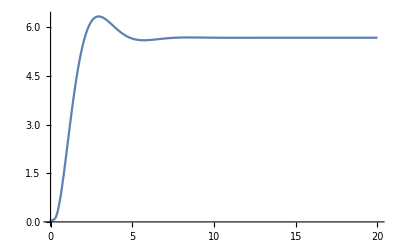

```mathematica
Plot[Evaluate[θ'[t]/.sol],{t,0,20},PlotRange->All]
```

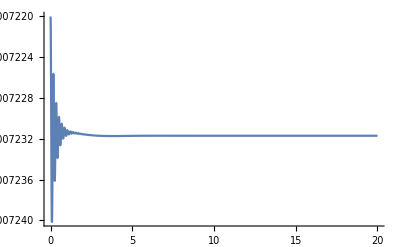

```mathematica
Plot[Evaluate[( y[t]-d1/2)//.SDATA/.sol],{t,0,20},PlotRange->All]
```

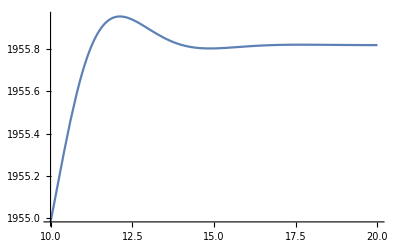

```mathematica
Plot[Evaluate[(( 𝕄⟦4,4⟧(2λ(ωd-θ'[t])+λ^2(ωd t - θ[t]))))//.SDATA/.sol],{t,10,20},PlotRange->All]
```

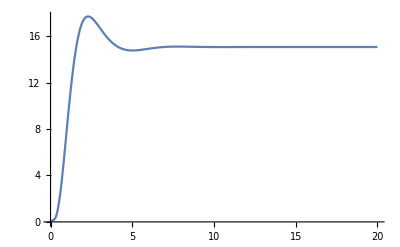

```mathematica
Plot[1/736.499 Evaluate[(θ'[t]( 𝕄⟦4,4⟧(2λ(ωd-θ'[t])+λ^2(ωd t - θ[t]))))//.SDATA/.sol],{t,0,20},PlotRange->All]
```

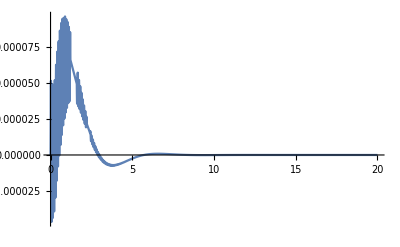

```mathematica
Plot[Evaluate[α[t]/.sol],{t,0,20},PlotRange->All]
```

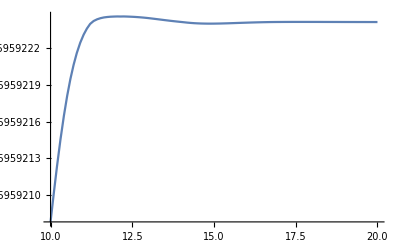

```mathematica
Plot[Evaluate[TE//.SDATA/.sol],{t,10,20},PlotRange->All]
```

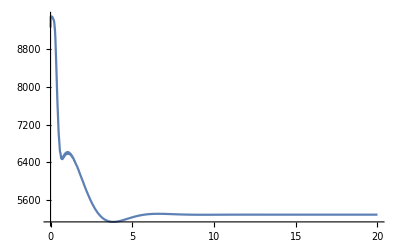

```mathematica
Plot[Evaluate[NT//.SDATA/.sol],{t,0,20},PlotRange->All]
```

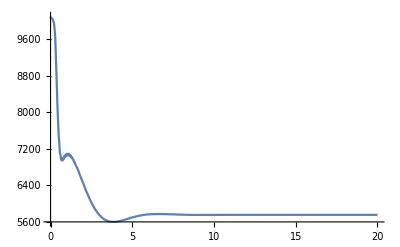

```mathematica
Plot[Evaluate[GT//.SDATA/.sol],{t,0,20},PlotRange->All]
```

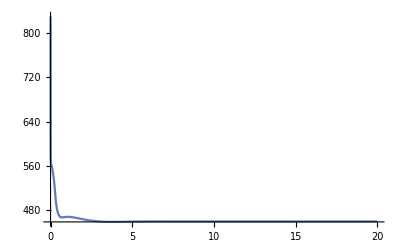

```mathematica
Plot[Evaluate[MR//.SDATA/.sol],{t,0,20},PlotRange->All]
```

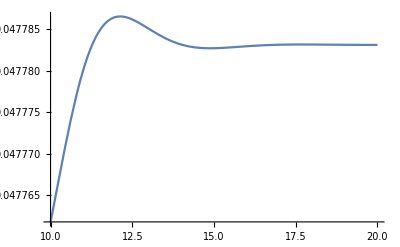

```mathematica
Plot[Evaluate[s//.SDATA/.sol],{t,10,20},PlotRange->All]
```

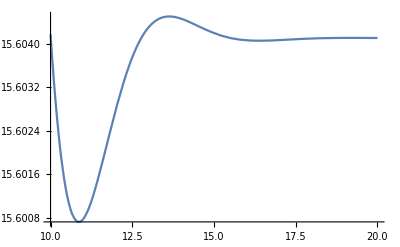

```mathematica
Plot[Evaluate[(GT x'[t])/736.499//.SDATA/.sol],{t,10,20},PlotRange->All]
```

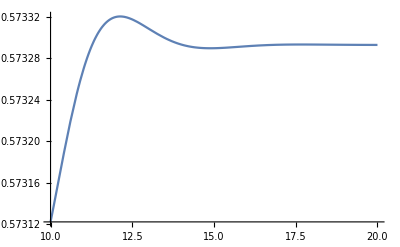

```mathematica
Plot[Evaluate[NTR//.SDATA/.sol],{t,10,20},PlotRange->All]
```